# Statistics of Linear Regression

## Theory for 0 - D

```mathematica
Stat0D[α_,lis_]:=TableForm[{{"Size","Mean","Var[Mean]","Confident Interval of sample Mean"},{Length[lis],Mean[lis],(√Variance[lis])/Length[lis],Mean[lis]+{Quantile[NormalDistribution[0,1],α/2](√Variance[lis])/Length[lis],-Quantile[NormalDistribution[0,1],α/2](√Variance[lis])/Length[lis]}}//N},TableDepth->2]
```

```mathematica
b={1.4,2,1.5};
```

```mathematica
Stat0D[0.05,b]
```

Size | Mean | Var[Mean] | Confident Interval of sample Mean
3. | 1.63333 | 0.107152 | {1.42332,1.84335}

## Theory for 1-D

the Sample is (X_i, Y_i)

the linear model is

Y_i=B_0+B_1 X_i+ϵ_i=OverHat[Y_i]+ϵ_i

The unbiased elstimator of B_0 and B_iare

OverHat[B_0]  and OverHat[B_1]

OverHat[Y_i]=OverHat[B_0]+OverHat[B_1]X_i

By least square method

OverHat[B_1]=(Σ(X_i-X^-)(Y_i-Y^-))/((Σ(X_i-X^-))^2)

OverHat[B_0]=Y^--OverHat[B_1]X^-

```mathematica
B1[lis_]:=Sum[(lis[[i,1]]-Mean[lis][[1]])(lis[[i,2]]-Mean[lis][[2]]),{i,1,Length[lis]}]/Sum[(lis[[i,1]]-Mean[lis][[1]])^2,{i,1,Length[lis]}]
B0[lis_]:=Mean[lis][[2]]-B1[lis]Mean[lis][[1]]
(* Sum of Square of Residual *)
RSS[lis_]:=Sum[(lis[[i,2]]-(B1[lis]lis[[i,1]]+B0[lis]))^2,{i,1,Length[lis]}]
(* Total Sum of square *)
TSS[lis_]:=Sum[(lis[[i,2]]-Mean[lis][[2]])^2,{i,1,Length[lis]}]
(* Sum of Square of Regression *)
RegSS[lis_]:=Sum[(Mean[lis][[2]]-(B1[lis]lis[[i,1]]+B0[lis]))^2,{i,1,Length[lis]}]
(* Correlation coefficient *)
Rsquare[lis_]:=RegSS[lis]/TSS[lis]//N
(* correlation *)
ρ[lis_]:=Correlation[lis]//N
(*plot *)
RegPlot1[lis_]:=Show[
Plot[B1[lis]x+B0[lis],{x,Min[Transpose[lis][[1]]]-1,Max[Transpose[lis][[1]]]+1},PlotRange->{Min[Transpose[lis][[2]]]-1,Max[Transpose[lis][[2]]]+1}],
ListPlot[lis,PlotStyle->Black],
Plot[Evaluate[LinearModelFit[lis,z,z]["MeanPredictionBands"]/.{z->y}],{y,0,10},PlotStyle->{Red,Blue},Filling->{1->{2}}]
]
(* Degree of freedom *)
DF[lis_]:=Length[lis]-2
(* variance of Yi- Ŷ *)
σ[lis_]:=√(Sum[(lis[[i,2]]-(B1[lis]lis[[i,1]]+B0[lis]))^2,{i,1,Length[lis]}]/(Length[lis]-2))
σB1[lis_]:=√(σ[lis]^2/Sum[(lis[[i,1]]-Mean[lis][[1]])^2,{i,1,Length[lis]}])
σB0[lis_]:=√((1/Length[lis]+(Mean[a][[1]])^2/Sum[(lis[[i,1]]-Mean[lis][[1]])^2,{i,1,Length[lis]}])σ[lis]^2)
CFB1[α_,lis_]:=B1[lis]+{Quantile[StudentTDistribution[Length[lis]-2],α/2]σB1[lis],-Quantile[StudentTDistribution[Length[lis]-2],α/2]σB1[lis]}
CFB0[α_,lis_]:=B0[lis]+{Quantile[StudentTDistribution[Length[lis]-2],α/2]σB0[lis],-Quantile[StudentTDistribution[Length[lis]-2],α/2]σB0[lis]}
```

## Example

```mathematica
a={{1,2},{2,3},{4,4},{5,6},{8,7},{9,10}};
```

```mathematica
LinearModelFit[a,x,x]["BestFitParameters"]
{B0[a],B1[a]}//N
```

{1.02295,0.891803}

{1.02295,0.891803}

```mathematica
LinearModelFit[a,x,x]["ANOVATableSumsOfSquares"]
{RegSS[a],RSS[a],TSS[a]}//N
```

{40.4284,2.90492,43.3333}

{40.4284,2.90492,43.3333}

```mathematica
LinearModelFit[a,x,x]["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
1 | 1.02295 | 0.674378 | {-0.849424,2.89533}
x | 0.891803 | 0.119526 | {0.559946,1.22366}

```mathematica
LinearModelFit[a,x,x]["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.02295 | 0.674378 | 1.51688 | 0.203893
x | 0.891803 | 0.119526 | 7.46116 | 0.00172436

```mathematica
LinearModelFit[a,x,x]["ParameterErrors"]
{σB0[a],σB1[a]}//N
```

{0.674378,0.119526}

{0.674378,0.119526}

```mathematica
LinearModelFit[a,x,x][x]
```

1.02295+0.891803 x

```mathematica
CFB1[0.05,a]
CFB0[0.05,a]
```

{0.559946,1.22366}

{-0.849424,2.89533}

```mathematica
LinearModelFit[a,x,x]["ANOVATable"]
(* DF = degree of Freedom *)
(* SS = Sum of square *)
(* MS = mean sum of square *)
(* F-Statistic = MSA/MSE *)
(* P- value = pobability of Null Hypothesis, B1 = 0 *)
```

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 40.4284 | 40.4284 | 55.6689 | 0.00172436
Error | 4 | 2.90492 | 0.72623 |  | 
Total | 5 | 43.3333 |  |  |

```mathematica
LinearModelFit[a,xx,xx]["MeanPredictionBands"]/.{xx->x}
```

```mathematica
(* Help Page *)
```

```mathematica
TableForm[LinearModelFit[a,x,x][{"BestFit",
"RSquared","ParameterTable","ParameterConfidenceIntervalTable","ANOVATable"}]]
```

1.02295+0.891803 x
0.932963
 | Estimate | Standard Error | t-Statistic | P-Value
1 | 1.02295 | 0.674378 | 1.51688 | 0.203893
x | 0.891803 | 0.119526 | 7.46116 | 0.00172436
 | Estimate | Standard Error | Confidence Interval
1 | 1.02295 | 0.674378 | {-0.849424,2.89533}
x | 0.891803 | 0.119526 | {0.559946,1.22366}
 | DF | SS | MS | F-Statistic | P-Value
x | 1 | 40.4284 | 40.4284 | 55.6689 | 0.00172436
Error | 4 | 2.90492 | 0.72623 |  | 
Total | 5 | 43.3333 |  |  |

```mathematica
LinearModelFit[a,x,x]["BIC"]
```

18.0504

```mathematica
Rsquare[a]
```

0.932963

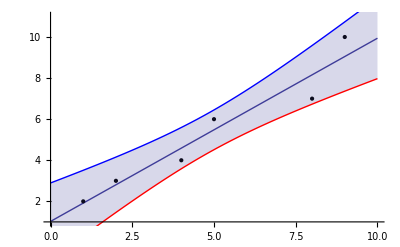

```mathematica
RegPlot[a]
```

## Theory for N- D

```mathematica
a2={{8.71,6.92,18.89},{6.05,5.97,15.08},{6.24,0.99,5.92},{8.25,3.37,11.39},{6.58,8.22,20.77},{4.14,9.,21.09},{4.35,9.94,24.32},{8.99,4.47,13.79},{2.82,3.91,10.68},{5.14,0.4,3.82}};
```

```mathematica
Remove[X]
```

```mathematica
Stats[lis_]:=Module[{g=Array[x,Dimensions[lis][[2]]-1]},
TableForm[
Join[{"Dimension of the list : "<>ToString[Dimensions[lis]]},
{"Fit Function : "<>ToString[LinearModelFit[lis,g,g]["BestFit"]]},
{"    R^2  : "<>ToString[LinearModelFit[lis,g,g]["RSquared"]]},
{"Adj.R^2  : "<>ToString[LinearModelFit[lis,g,g]["AdjustedRSquared"]]},
LinearModelFit[lis,g,g][{"ParameterTable","ParameterConfidenceIntervalTable","ANOVATable"}]]]
]
```

```mathematica
a3=Table[{RandomInteger[{0,10}],RandomInteger[{10,20}]},{i,1,20}];
```

```mathematica
a4
```

{{1,4},{2,5},{3,6.1},{4,6},{5,8},{6,9},{7,10.5}}

```mathematica
Stats[a4]
```

Dimension of the list : {7, 2}
Fit Function : 2.88571 + 0.996429 x[1]
    R^2  : 0.968846
Adj.R^2  : 0.962616
 | Estimate | Standard Error | t-Statistic | P-Value
1 | 2.88571 | 0.357357 | 8.07516 | 0.000471751
x[1] | 0.996429 | 0.0799075 | 12.4698 | 0.0000588222
 | Estimate | Standard Error | Confidence Interval
1 | 2.88571 | 0.357357 | {1.9671,3.80433}
x[1] | 0.996429 | 0.0799075 | {0.79102,1.20184}
 | DF | SS | MS | F-Statistic | P-Value
x[1] | 1 | 27.8004 | 27.8004 | 155.495 | 0.0000588222
Error | 5 | 0.893929 | 0.178786 |  | 
Total | 6 | 28.6943 |  |  |

```mathematica
(* Pvalue for F-Statistic *)
1-CDF[FRatioDistribution[1,5],155.495]
```

0.0000588226

```mathematica
1-CDF[StudentTDistribution[2.8857,0.35736,1],8.075]
```

0.0218858

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
StudentTCI[0,1,2]
StudentTPValue[4.30265,2,TwoSided->True]
StudentTCI[0.786,0.27664,5]
```

{-4.30265,4.30265}

TwoSidedPValue→0.0500001

{0.0748742,1.49713}

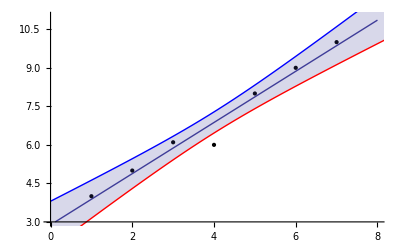

Dimension of the list : {7, 2}
Fit Function : 2.88571 + 0.996429 x[1]
R^2  : 0.968846
 | Estimate | Standard Error | t-Statistic | P-Value
1 | 2.88571 | 0.357357 | 8.07516 | 0.000471751
x[1] | 0.996429 | 0.0799075 | 12.4698 | 0.0000588222
 | Estimate | Standard Error | Confidence Interval
1 | 2.88571 | 0.357357 | {1.9671,3.80433}
x[1] | 0.996429 | 0.0799075 | {0.79102,1.20184}
 | DF | SS | MS | F-Statistic | P-Value
x[1] | 1 | 27.8004 | 27.8004 | 155.495 | 0.0000588222
Error | 5 | 0.893929 | 0.178786 |  | 
Total | 6 | 28.6943 |  |  |

```mathematica
a4={{1,4},{2,5},{3,6.1},{4,6},{5,8},{6,9},{7,10}};
RegPlot1[a4]
Stats[a4]
```

## Multi - demension

Dimension of the list : {7, 2}
Fit Function : 1.15714 + 0.928571 X[1]
R^2  : 0.976089
 | Estimate | Standard Error | t-Statistic | P-Value
1 | 1.15714 | 0.290671 | 3.98093 | 0.010521
X[1] | 0.928571 | 0.0649961 | 14.2866 | 0.0000302783
 | Estimate | Standard Error | Confidence Interval
1 | 1.15714 | 0.290671 | {0.409949,1.90434}
X[1] | 0.928571 | 0.0649961 | {0.761494,1.09565}
 | DF | SS | MS | F-Statistic | P-Value
X[1] | 1 | 24.1429 | 24.1429 | 204.106 | 0.0000302783
Error | 5 | 0.591429 | 0.118286 |  | 
Total | 6 | 24.7343 |  |  |

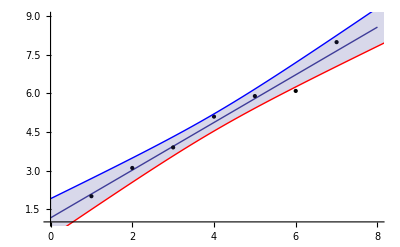

```mathematica
aa={{1,2},{2,3.1},{3,3.9},{4,5.1},{5,5.9},{6,6.1},{7,8}};
Stats[aa]
RegPlot1[aa]
```

```mathematica
x=Transpose[Join[{Table[1,{i,1,Length[aa]}]},{Transpose[aa][[1]]}]];
Y=Transpose[aa][[2]]
B=Inverse[Transpose[x].x].Transpose[x].Y
Ŷ=x.Inverse[Transpose[x].x].Transpose[x].Y
σsquare=Sum[(Y[[i]]-Ŷ[[i]])^2,{i,1,Length[Y]}]/(Length[aa]-2)
σB=Table[√((Inverse[Transpose[x].x]σsquare)[[i,i]]),{i,1,Length[B]}]
```

{2,3.1,3.9,5.1,5.9,6.1,8}

{1.15714,0.928571}

{2.08571,3.01429,3.94286,4.87143,5.8,6.72857,7.65714}

0.118286

{0.290671,0.0649961}

```mathematica
x
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7}}

```mathematica
xY=Transpose[Join[Transpose[x],{Y}]]
```

{{1,1,2},{1,2,3.1},{1,3,3.9},{1,4,5.1},{1,5,5.9},{1,6,6.1},{1,7,8}}

```mathematica
LinearModelFit[aa,z,z]
```

FittedModel[1.15714+0.928571 z]

## MWDC

```mathematica
h[z1_,z2_,z3_,z4_,z5_,z6_]:={
{z1,1,0,0},
{z2,1,0,0},
{0.8z3 , 0.8,0.6 z3 ,0.6},
{0.8z4 , 0.8, 0.6z4 ,0.6},
{0.8z5, 0.8, -0.6z5 ,-0.6},
{0.8z6, 0.8, -0.6z6 ,-0.6}
}
hh=h[0,8,16,24,32,48];
```

{-0.0239795,4.03627,-0.0397818,-5.75359}

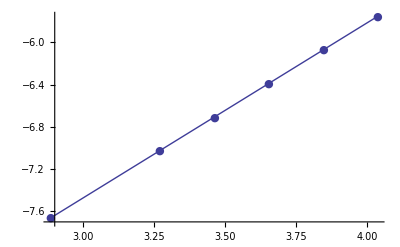

{-0.0270014,4.03962,-0.0451864,-5.6214}

0.0286929

{0.00959347,0.136236,0.0260943,0.698224}

-0.0270014 a-0.0451864 b+4.03962 x0-5.6214 y0
0.999547
 | Estimate | Standard Error | t-Statistic | P-Value
a | -0.0270014 | 0.00959347 | -2.81456 | 0.106455
x0 | 4.03962 | 0.136236 | 29.6515 | 0.00113544
b | -0.0451864 | 0.0260943 | -1.73166 | 0.225473
y0 | -5.6214 | 0.698224 | -8.051 | 0.0150796
 | Estimate | Standard Error | Confidence Interval
a | -0.0270014 | 0.00959347 | {-0.0682788,0.014276}
x0 | 4.03962 | 0.136236 | {3.45344,4.6258}
b | -0.0451864 | 0.0260943 | {-0.157461,0.0670882}
y0 | -5.6214 | 0.698224 | {-8.62561,-2.61718}
 | DF | SS | MS | F-Statistic | P-Value
a | 1 | 68.1376 | 68.1376 | 2374.72 | 0.000420837
x0 | 1 | 6.71399 | 6.71399 | 233.995 | 0.0042464
b | 1 | 49.9554 | 49.9554 | 1741.04 | 0.000573876
y0 | 1 | 1.85983 | 1.85983 | 64.8185 | 0.0150796
Error | 2 | 0.0573858 | 0.0286929 |  | 
Total | 6 | 126.724 |  |  |

```mathematica
(* general a ray *)
p={RandomReal[{-0.2,0.2}],RandomReal[{-7,7}],RandomReal[{-0.2,0.2}],RandomReal[{-7,7}]}
kR=0.2Table[RandomReal[{-1,1}],{i,1,6}];
ray[z_]:={p[[1]]z+p[[2]],p[[3]]z+p[[4]]}
ListPlot[Table[ray[z],{z,{0,8,16,24,32,48}}],Joined->True,PlotMarkers->{Automatic,Medium}]
Y={ray[0][[1]],
ray[8][[1]],
ray[16][[1]]0.8+ray[16][[2]]0.6,
Norm[ray[24]]Cos[ArcCos[0.8]-ArcTan[ray[24][[1]],ray[24][[2]]]],
Norm[ray[32]]Cos[-ArcCos[0.8]-ArcTan[ray[32][[1]],ray[32][[2]]]],
Norm[ray[48]]Cos[-ArcCos[0.8]-ArcTan[ray[48][[1]],ray[48][[2]]]]
}+kR;
B=Inverse[Transpose[hh].hh].Transpose[hh].Y
Ya=hh.Inverse[Transpose[hh].hh].Transpose[hh].Y;
σsquare=Sum[(Y[[i]]-Ya[[i]])^2,{i,1,Length[Y]}]/2
σB=Table[√((Inverse[Transpose[hh].hh]σsquare)[[i,i]]),{i,1,Length[B]}]
TableForm[LinearModelFit[{hh,Y},{a,x0,b,y0}][{"BestFit","RSquared","ParameterTable","ParameterConfidenceIntervalTable","ANOVATable"}]]
```